## Exercise 2—Direction Fields

## Exercise 1

Match the direction field to the differential equation:

y'(x)=y(x) x

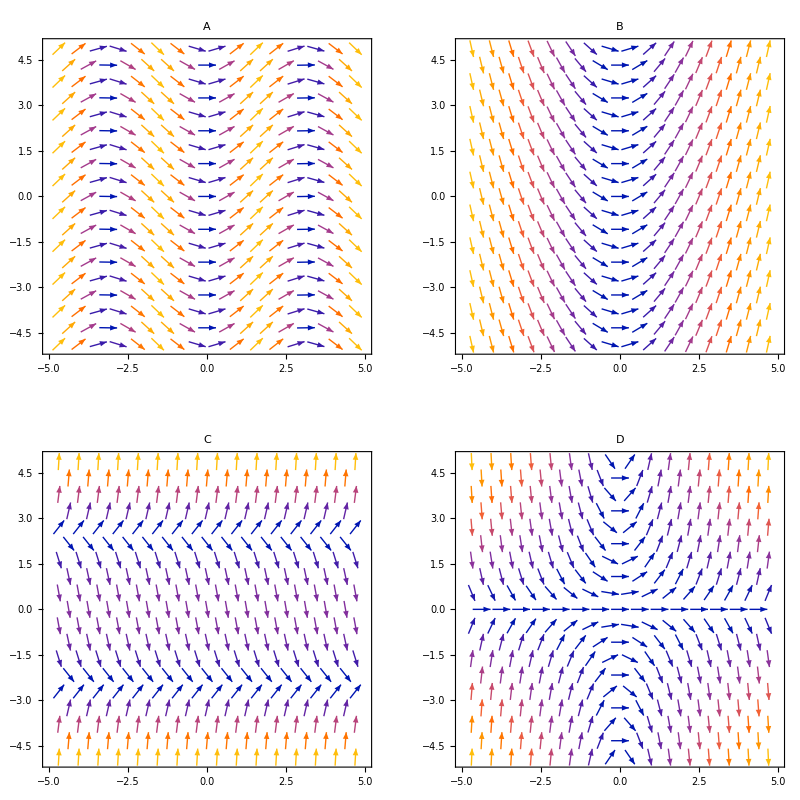

```mathematica
GraphicsGrid[{
{
VectorPlot[{1,Sin[x]},{x,-5,5},{y,-5,5},PlotLabel->Style["A",18,Bold],ImagePadding->20],
VectorPlot[{1,x},{x,-5,5},{y,-5,5},PlotLabel->Style["B",18,Bold],ImagePadding->20]
},
{
VectorPlot[{1,y^2-6},{x,-5,5},{y,-5,5},PlotLabel->Style["C",18,Bold],ImagePadding->20],
VectorPlot[{1,y*x},{x,-5,5},{y,-5,5},PlotLabel->Style["D",18,Bold],ImagePadding->20]}
}]
```

### Solution

The best place to start is to look where the derivative is zero, which is whenever y=0 or x=0.

It can be seen that only direction field D satisfies this property.

Verify this using the function VectorPlot:

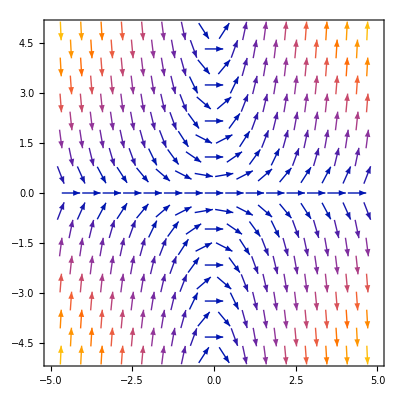

```mathematica
VectorPlot[{1,y*x},{x,-5,5},{y,-5,5}]
```

## Exercise 2

Match the direction field to the differential equation:

y'(x)=(y(x))^2-2y(x)-8

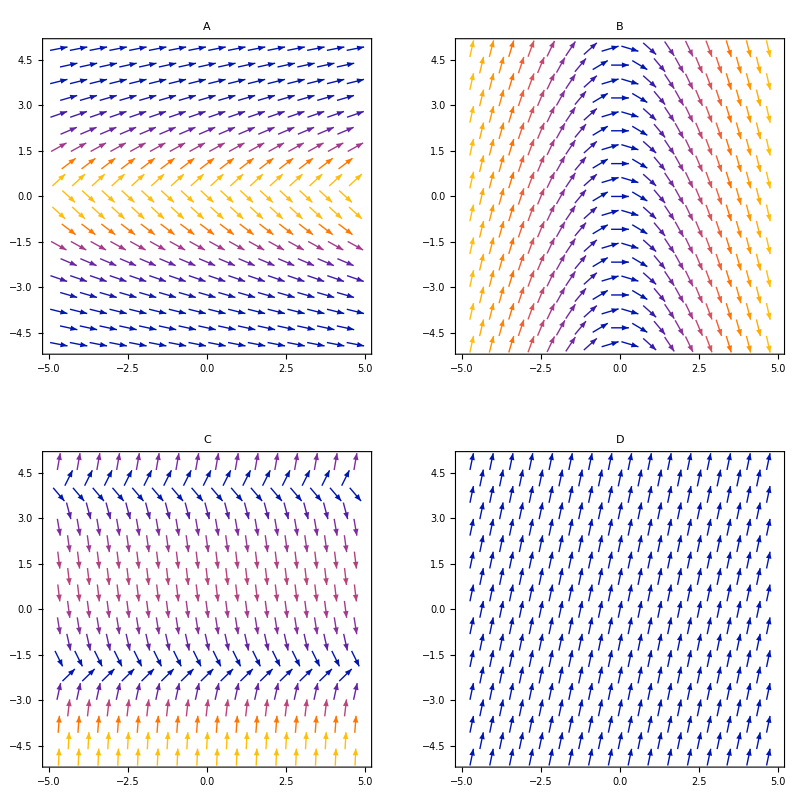

```mathematica
GraphicsGrid[{
{
VectorPlot[{1,Sin[1/y]},{x,-5,5},{y,-5,5},PlotLabel->Style["A",18,Bold],ImagePadding->20],VectorPlot[{1,-x},{x,-5,5},{y,-5,5},PlotLabel->Style["B",18,Bold],ImagePadding->20]
},
{
VectorPlot[{1,y^2-2y-8},{x,-5,5},{y,-5,5},PlotLabel->Style["C",18,Bold],ImagePadding->20],VectorPlot[{1,5},{x,-5,5},{y,-5,5},PlotLabel->Style["D",18,Bold],ImagePadding->20]
}
}]
```

### Solution

The best place to start is to look where the derivative is zero, which is whenever y=4 or y=2.

It can be seen that only direction field C satisfies this property.

This can be verified using the function VectorPlot:

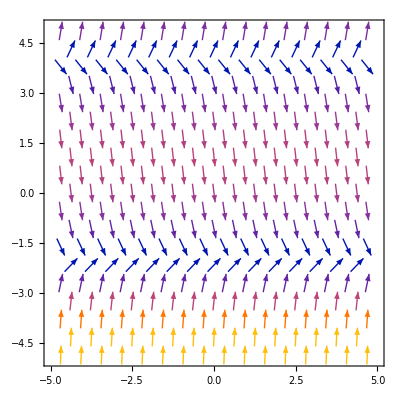

```mathematica
VectorPlot[{1,y^2-2y-8},{x,-5,5},{y,-5,5}]
```

## Exercise 3

Describe how solutions behave as t→∞ for the differential equation:

r'(t)=5r(t)+3

### Solution

When the derivative is zero,  r(t)=-3/5.

This is described as an equilibrium solution and can be verified using VectorPlot:

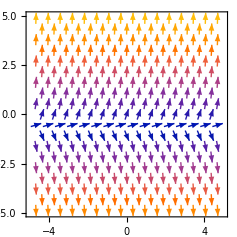

```mathematica
VectorPlot[{1,5r+3},{t,-5,5},{r,-5,5}]
```

As can be seen, this does in fact agree with the inference that r(t)=-3/5 is an equilibrium solution.

With the information from VectorPlot, it can be seen that this is in fact an unstable equilibrium solution.

As time progresses, solutions tend to diverge from this equilibrium solution.

That makes  -3/5 an unstable equilibrium point.

## Exercise 4

Describe how solutions behave as t→∞ for the differential equation:

r'(t)=(r(t))^2+1

### Solution

For this differential equation, there is no value of r(t) that satisfies (r(t))^2+1=0.

Thus there is no equilibrium solution.

You can verify this using VectorPlot:

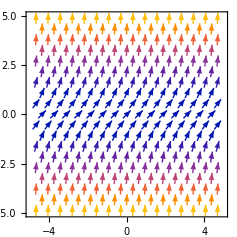

```mathematica
VectorPlot[{1,r^2+1},{t,-5,5},{r,-5,5}]
```

All solutions diverge to positive infinity because the derivative is always positive.

## Exercise 5

Construct a differential equation that models a spherical raindrop that evaporates at a rate linearly proportional to its surface area.

### Solution

Use the information given in the problem to identify the most important components of the equation.

There is an unknown variable, v(t), which is the volume of the raindrop at time t.

The volume of the raindrop changes as a function of time. This can be written as the derivative of the volume as v'(t).

You know that the volume changes at a rate linearly proportional to its surface area, and that the surface area and volume are given by the following expressions:

Surface Area=4 π r^2

Volume=4/3 π r^3

With r(t) being the radius of the sphere at time t, the surface area at time t can be written as 3(v(t))/(r(t)).

Therefore, using α as the linear proportionality constant, the differential relation can be written as:

v'(t)=α*3*(v(t))/(r(t))

## Exercise 3—Solutions to Differential Equations

## Exercise 1

Solve the following differential equation:

y'(x)=2y(x)

### Solution

First, divide both sides by y(x) and multiply by ⅆx to write the equation as:

(ⅆy(x))/(y(x))=2ⅆx

Integrate the left-hand side with respect to y(x) and the right-hand side with respect to x:

```mathematica
sln=Integrate[1/y[x],y[x]]==Integrate[2,x,GeneratedParameters->C]
```

Log[y[x]]==2 x+C[1]

Solve for the unknown function y(x):

```mathematica
Solve[sln,y[x],Reals]
```

{{y[x]→ⅇ^(2 x+C[1])}}

Verify the answer using DSolveValue:

```mathematica
DSolveValue[eqn,y[x],x]
```

ⅇ^(2 x) C[1]

Since the e^C_1 term in the first result and the C_1 term in the second result are both just an arbitrary constant, the two results agree.

## Exercise 2

Solve the following differential equation:

y'(x)=5y(x)+3

### Solution

First, divide both sides by 5y(x)+3 and multiply by ⅆx to arrive at:

(ⅆy(x))/(5y(x)+3)=ⅆx

Integrate the left-hand side with respect to y(x) and the right-hand side with respect to x:

```mathematica
sln=Integrate[1/(5y[x]+3),y[x]]==Integrate[1,x,GeneratedParameters->C]
```

1/5 Log[3+5 y[x]]==x+C[1]

Solve for the unknown function y(x):

```mathematica
Solve[sln,y[x],Reals]//Expand
```

{{y[x]→-3/5+1/5 ⅇ^(5 x+5 C[1])}}

Verify your answer using DSolveValue:

```mathematica
DSolveValue[eqn,y[x],x]
```

-3/5+ⅇ^(5 x) C[1]

Since 1/5 e^(5 C_1) in the first result and C_1 in the second result are just two arbitrary constants, the two results are equivalent.

## Exercise 3

Solve the following initial value problem:

y'(x)=2 y(x)+1

y(0)=0

### Solution

Divide by 2 y(x)+1, multiply by ⅆx, then integrate both sides, as was done in Exercises 1 and 2:

```mathematica
sln=Integrate[1/(2 y[x]+1),y[x]]==Integrate[1,x,GeneratedParameters->C]
```

1/2 Log[1+2 y[x]]==x+C[1]

Solve for y(x):

```mathematica
generalSolution=y[x]/.Solve[sln,y[x],Reals][[1]]
```

1/2 (-1+ⅇ^(2 x+2 C[1]))

Now that you have the general solution, find the value for C_1 that makes the general solution satisfy the initial condition that the solution equals 0 at x=0:

```mathematica
initialCondition=(generalSolution/.x->0)==0
```

1/2 (-1+ⅇ^(2 C[1]))==0

Solve the equation for C_1:

```mathematica
constant=Solve[initialCondition,C[1],Reals][[1]]
```

{C[1]→0}

Substitute this value for C_1 into the general solution to solve the initial value problem:

```mathematica
(generalSolution/.constant)
```

1/2 (-1+ⅇ^(2 x))

Verify the result using DSolveValue:

```mathematica
DSolveValue[{y'[x]==2y[x]+1,y[0]==0},y[x],x]
```

1/2 (-1+ⅇ^(2 x))

## Exercise 4

Consider the differential equation:

y'(t)=0.5y(t)

Describe the behavior of solutions to this equation based on the initial condition:

y(0)=y_0

### Solution

In order to make conclusions about the behavior of solutions, use a direction field:

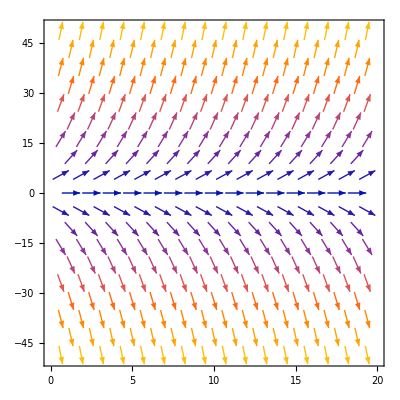

```mathematica
VectorPlot[{1,0.5 y},{t,0,20},{y,-50,50}]
```

From this direction field, it is seen that solutions with positive initial conditions tend to diverge to positive infinity and solutions with negative initial conditions tend to diverge to negative infinity.

There is an unstable equilibrium solution at y(t)=0.

## Exercise 5

Solve the differential equation:

y'(x)=(y(x))/10-15

Plot the solutions for each initial condition:

y(0)=50,100,150,200,250.

### Solution

First, solve the differential equation as described in Exercises 1 and 2:

```mathematica
sln=Integrate[1/(y[x]/10-15),y[x]]==Integrate[1,x,GeneratedParameters->C]
```

10 Log[-150+y[x]]==x+C[1]

Solve for the unknown function y(x):

```mathematica
Solve[sln,y[x],Reals]
```

{{y[x]→150+ⅇ^(x/10+C[1]/10)}}

Using C=e^(C_1/10) as the arbitrary constant, the general solution is:

y(x)=150+C e^(x/10)

Verify with DSolveValue:

```mathematica
DSolveValue[y'[x]==y[x]/10-15,y[x],x]
```

150+ⅇ^(x/10) C[1]

The plots for each initial condition are shown in the following:

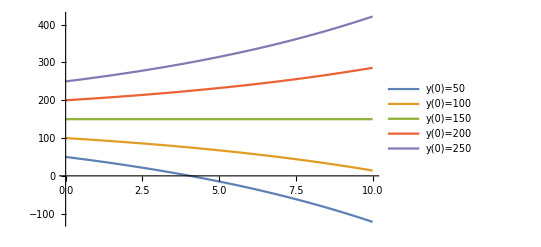

```mathematica
Plot[Evaluate[Table[150+C*Exp[x/10],{C,-100,100,50}]],{x,0,10},PlotLegends->{"y(0)=50","y(0)=100","y(0)=150","y(0)=200","y(0)=250"}]
```

## Exercise 4—Classification of Differential Equations

## Exercise 1

Determine the order of the following differential equations:

-y'(x)=x^7

y''(x)*x=sin(x)

-y'(x)+y''(x)+(y(x))^6+y''''(x)=x^7

### Solution

In order to solve this problem, it is only necessary to find the order of the highest derivative. This is the definition of the order of a differential equation.

1. It can be seen that the highest order of derivatives that appears in the equation is 1, so this is a first-order differential equation.

2. It can be seen that the highest order of derivatives that appears in the equation is 2, so this is a second-order differential equation.

3. It can be seen that the highest order of derivatives that appears in the equation is 4, so this is a fourth-order differential equation.

## Exercise 2

Classify the following equations as linear or nonlinear:

-y'(x)=x^7

y''(x)*x=sin(x)

-y'(x)+y''(x)+(y(x))^6+y''''(x)=x^7

### Solution

1. This equation is a linear differential equation.

2. This equation is a linear differential equation.

3. This equation is nonlinear due to the term (y(x))^6.

## Exercise 3

Verify that sin(x) is the solution to the following initial value problem:

y''(x)=-y(x)

y(0)=0

y'(0)=1

### Solution

You can use DSolveValue to verify the result by specifying the initial conditions:

```mathematica
DSolveValue[{y''[x]==-y[x],y[0]==0,y'[0]==1},y[x],x]
```

Sin[x]

This can also be done manually by checking that sin(x) satisfies both initial conditions and the differential equation.

First, check that sin(x) is 0 when x=0:

```mathematica
Sin[0]==0
```

True

Next, check the first derivative equals 1 at x=0:

```mathematica
D[Sin[x],x]/.x->0
```

1

Finally, verify that sin(x) is the solution to the differential equation itself:

```mathematica
(y''[x]==-y[x])/.y->Function[x,Sin[x]]
```

True

## Exercise 4

Verify that 3x+x^2 is a solution to the differential equation:

x y'(x)=y(x)+x^2

### Solution

To verify that 3x+x^2 is a solution, substitute this solution back into the equation to see if the function satisfies the equation:

```mathematica
(x*y'[x]==y[x]+x^2)/.y->Function[x,3 x+x^2]//Simplify
```

True

## Exercise 5

Verify that e^-t sin(x) is a solution to this partial differential equation:

(∂u(x,t))/(∂t)=(∂^2 u(x,t))/(∂x^2)

### Solution

To verify that e^-t sin(x) is a solution, substitute this solution back into the equation to see if the function satisfies the equation:

```mathematica
(D[u[x,t],t]==D[u[x,t],{x,2}])/.u->Function[{x,t},Exp[-t]Sin[x]]
```

True